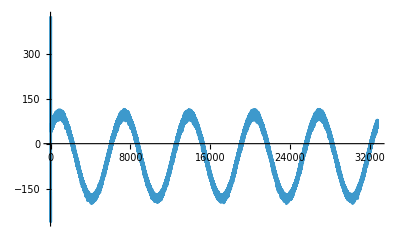

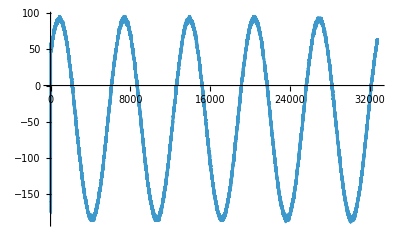

283.202

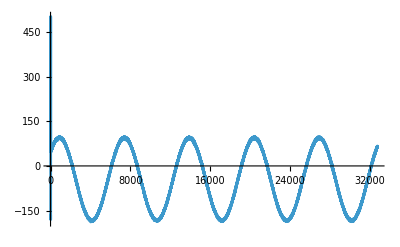

691.381

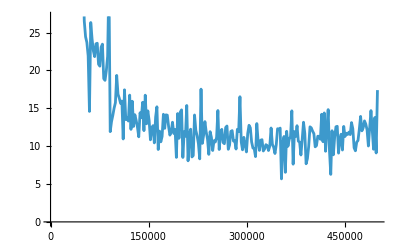

{{3046875/256,328008.,115968.},{19296875/512,33135.5,11715.2},{45703125/512,23092.2,8164.34}}

```mathematica
fs=65*10^6;

data=First@Import["/home/shaoyafan/develop/wavegen/res/data/raw_adc.txt","CSV"];
n=Length[data];
ListLinePlot[data]
medData=MedianFilter[data,7];
ListLinePlot[medData]
Max[medData]-Min[medData]
firData=LowpassFilter[data,550000,7,SampleRate->65000000];
ListLinePlot[firData]
Max[firData]-Min[firData]
fft=Fourier[data];
spectrum=Abs[fft];
freq=Range[0,n-1] fs/n;
half=Floor[n/2];
freqHalf=freq[[1;;half]];
specHalf=spectrum[[1;;half]];
band=Pick[Range[Length[freqHalf]],Thread[10000<=freqHalf<=500000]];
freqBand=freqHalf[[band]];
specBand=specHalf[[band]];
ListLinePlot[Transpose[{freqBand,specBand}]]
peaks=FindPeaks[specBand];
peaksSorted=Reverse@SortBy[peaks,Last];
components=Take[peaksSorted,UpTo[3]];
idx=components[[All,1]];
peakFreq=freqBand[[idx]];
peakAmplitude=2 specBand[[idx]] Sqrt[n];
vpp=2 peakAmplitude;
vrms=peakAmplitude/Sqrt[2];
result=Transpose[{peakFreq,vpp,vrms}]
```